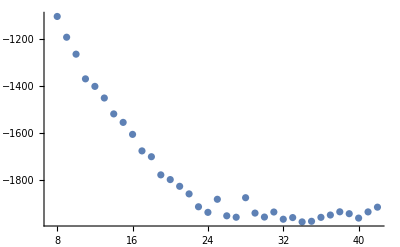

```mathematica
filen="/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat";
data=Import[filen,"Table"][[2;;]];
ListPlot[data[[All,{1,3}]]]
```

-9213.39

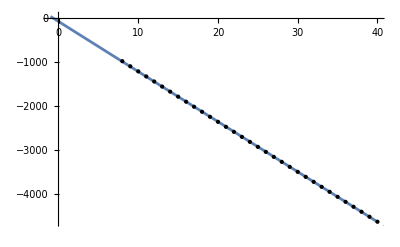

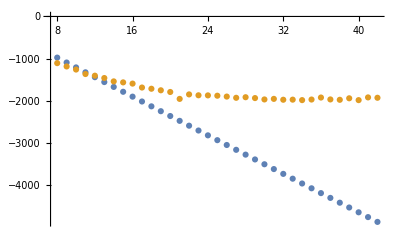

```mathematica
filen="/home/kirscher/Documents/vault/Vorlesungen/num_methods/lec_ex0_b2.22.dat";
data=Import[filen,"Table"][[2;;]];
dc=Transpose[{data[[All,1]],data[[All,2]]}];
dd=Transpose[{data[[All,1]],data[[All,3]]}];

line=Fit[dc,{1,x},x];
line/.x->80
Plot[line,{x,-1,40},Epilog->Point[dc]]
ListPlot[{dc,dd}]
```

λ    C0

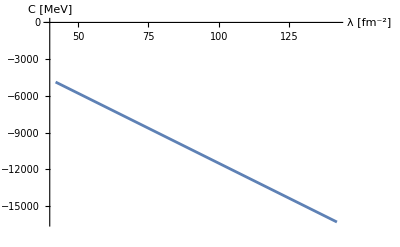

```mathematica
Λl=Range[42,142,1.0];
LEC0s={};
res={};
Print["λ    C0"]
Do[{λ=Λl⟦j⟧;
C0=line/.x->λ;
AppendTo[LEC0s,    { StringPadRight[ToString[λ],6],StringPadRight[ToString[C0],12]}];
AppendTo[res,{λ,C0}];
(*Print[StringPadRight[ToString[λ],5]<>"  "<>StringPadRight[ToString[aleph^-1],7]<>"  "<>StringPadRight[ToString[C0],7] ];*)
},{j,Length[Λl]}];
list=ExportString[LEC0s,"Table"];
WriteString["/home/kirscher/kette_repo/limit_cycles/manuscript/graphs/tmpLECs.dat",list];
Close["/home/kirscher/kette_repo/limit_cycles/manuscript/graphs/tmpLECs.dat"];
ListPlot[res,Joined->True,AxesLabel->{"λ [fm^-2]","C [MeV]"}]
```